# Rapport Inlämningsuppgift 3, Projekt Grupp 17

Malcolm Liljedahl, IX1307, malcolml@kth.se
Ted Melander, IX1307, tedme@kth.se

Uppgift 1: Trafikflöde

## Uppgifter och Resultat

### Uppgift

Den här uppgiften går ut på och visa hur man kan använda linjära ekvationssystem för att studera trafikflödet genom ett trafiksystem. Trafiksystemet består av gator och korsningar där gatorna möts. Varje gata har ett visst flöde, som mäts i fordon per tidenhet. Vi skall beräkna trafikflödet för alla gatorna i trafiksystemet, givet flödet in till trafiksystemet.  Vi gör ett  viktigt antagande: Trafikflödet bevaras i varje korsning. Det betyder att ett fordon som når en korsning måste fortsätta genom trafiksystemet. Ett positivt värde på flödet flyter i pilens riktning och ett negativt flöde flyter i motsatt riktning.

a) Är vårt antagande om att flödet bevaras giltigt? När kan antagandet vara felaktigt?
b) Vilka andra förenklingar har vi antagit?

Studera vägssystemet i figur 1. Siffrorna anger trafikflödena i fordon per timme. Alla vägar är enkelriktade och trafiken följer pilarnas riktning.
b) Ställ upp ekvationssystemet.
c) Bestäm trafikflödet för vägsystemet.
d) Om trafikflödet för en av x, y, z eller w begränsas till 100 fordon per timme på grund av vägarbete. Vad blir trafikflödet för de andra vägarna?

### Resultat

1.A) 
Nej det är det självklart inte, trafikflödet kommer variera ganska stort genom dagen om man jämför med ett typiskt vägsystem. Det är rusningstrafik under vissa tidpunkter på dagen och andra kan det vara helt stilla. Man kan till exempel inte jämföra trafiken under rusnignstimmarna med trafiken under natten. Samt om man antar att bilar inte kan avlägsna eller ansluta sig så kan trafikflödet ändå påverkas av externa faktorer såsom bilolyckor, nödvändigt att kunna flytta sig för till exempel utrycksningsfordon o.s.v.


1.B) 
Vi har antagit att bilar varken kan avlägsna sig eller ansluta sig till trafikflödet. Uppgiften tar inte upp att bilar kan stanna men det nämns att bilar ej kan avlägsna sig ifrån trafiken. Modellen antar också att alla bilar följer lagen och att ingen bil kan göra en u-sväng alternativt kör mottrafiken på en enkelriktad gata.

1.C) Ställ upp ekvationssystemet

A.) xw=x +w =431

B.) xy=x+y=255

C.) zy=z+y=340

D.) wz=w+z=516

-Graphics-

1.D) Bestäm trafikflödet i korsningen

Då vi inte vet exakt hur många bilar som befinner sig på varje väg så kan vi endast räkna ut förhållandet mellan de olika vägarna, vi kan inte räkna ut trafikflödet. Då bil variablerna x,y,z och w är okända.

Förhållandet till x:
y = 255 - x, 
z = 85 + x, 
w = 431 - x

Förhållandet till y:
z = 340 - y
w = 176 + y
x = 255 - y

Förhållandet till z:
w =516 - z
x = -85 + z
y = 340 - z

Förhållandet till w:
x = 431 - w
y = -176 + w
z = 516 - w

1.E) Om trafikflödet för en av x, y, z eller w begränsas till 100 fordon per timme på grund av vägarbete. Vad blir trafikflödet för de andra vägarna?

Då trafikflödet på gata x begränsas till 100 så påverkas det resterande gatorna enligt följande:

y=155

z=185

w=331

-Graphics-

Då trafikflödet på gata y begränsas till 100 så påverkas det resterande gatorna enligt följande:

x=155

z=240

w=276

-Graphics-

Då trafikflödet på gata z begränsas till 100 så påverkas det resterande gatorna enligt följande:

x=15

y=240

w=416

-Graphics-

Då trafikflödet på gata w begränsas till 100 så påverkas det resterande gatorna enligt följande:

x=331

y=-76

z=416

-Graphics-

Här kan man se att modellen faller kort, då y värdet blir negativt. Trafikflödet kan inte bli negativt här då det kan tolkas som en riktning, för alla vägar är enkelriktade.

Trots uppgiftens formulering så antas det att trafikflödet begränsas till exakt 100 bilar och inte mindre än 100.

## Kod

1.C) Ställ upp ekvationssystemet

Sammansatta variabler deklareras som variabelnamn  för funktionenerna för lättare hantering.

A.)

```mathematica
xw=x +w == 431
```

w+x==431

B.)

```mathematica
xy=x+y==255
```

x+y==255

C.)

```mathematica
zy=z+y==340
```

y+z==340

D.)

```mathematica
wz=w+z==516
```

w+z==516

1.D) Bestäm trafikflödet i korsningen

Med hjälp av verktyget Reduce så kan vi få fram vägarnas förhållande till varandra.

```mathematica
Reduce[{xw, xy, zy, wz},{x,y,z,w}]
```

y==255-x&&z==85+x&&w==431-x

```mathematica
Reduce[{xw, xy, zy, wz},{y,x,z,w}]
```

x==255-y&&z==340-y&&w==176+y

```mathematica
Reduce[{xw, xy, zy, wz},{z,w,x,y}]
```

w==516-z&&x==-85+z&&y==340-z

```mathematica
Reduce[{xw, xy, zy, wz},{w,x,y,z}]
```

x==431-w&&y==-176+w&&z==516-w

1.E) Om trafikflödet för en av x, y, z eller w begränsas till 100 fordon per timme på grund av vägarbete. Vad blir trafikflödet för de andra vägarna?

För x=100:

```mathematica
Reduce[{xw, xy, zy, wz,x==100},{x,y,z,w}]
```

x==100&&y==155&&z==185&&w==331

För y=100:

```mathematica
Reduce[{xw, xy, zy, wz,y==100},{x,y,z,w}]
```

x==155&&y==100&&z==240&&w==276

För z=100:

```mathematica
Reduce[{xw, xy, zy, wz,z==100},{x,y,z,w}]
```

x==15&&y==240&&z==100&&w==416

För w=100:

```mathematica
Reduce[{xw, xy, zy, wz,w==100},{x,y,z,w}]
```

x==331&&y==-76&&z==416&&w==100

Trots uppgiftens formulering så antas det att trafikflödet begränsas till exakt 100 bilar och inte mindre än 100.

Uppgift 2: Kaniner

## Uppgifter och Resultat

### Uppgifter

Leonardo av Pisa, även känd som Fibonacci (circa 1170-1250) skapade en av de äldsta matematiska modellerna av förökning. Han modellerade förökning av kaniner. Genom att modellera kaninpar kunde han undvika att ta hänsyn till individuella kaniner av olika kön. Modellen beskriver förökningen av kaniner från månad n=1 där p_n är antal kaniner vid månad n. När en kanin föds, så är den en unge under en månad och sedan förökar sig kaninparen varje månad. Antal kaniner kan då beskrivs av en differensekvation:

p_(n+2)=p_(n+1)+p_n

där vi antar att vi har bara ett kaninpar vid månad n=1, dvs intialvärdena är p_1=1 och p_2=1. Vilket betyder att p_3=2,  p_4=3 och p_5=5.

a) Beräkna talföljden och rita en graf över den.
b) Undersök talföljden och diskutera tillväxtakten.
c) Vilka begränsningar har modellen?
d) Hur kan man förbättra modellen?

### Resultat

2.A) Beräkna talföljden och rita en graf över den.

Såhär ser talföljden ut under de första 24 månaderna : 

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368}

Så här kommer förökningen se ut under de kommande 24 månaderna

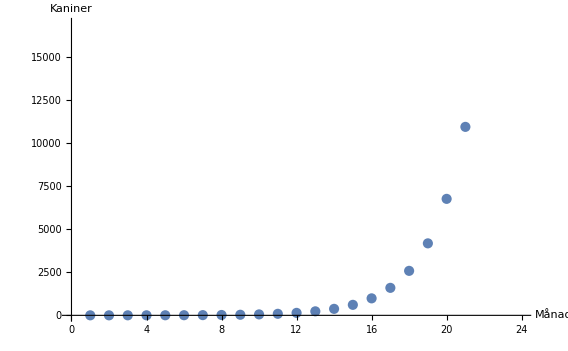

Om man vill granska förökningen inom mindre intervall än månader så kan man illustrera den genom en linje istället.

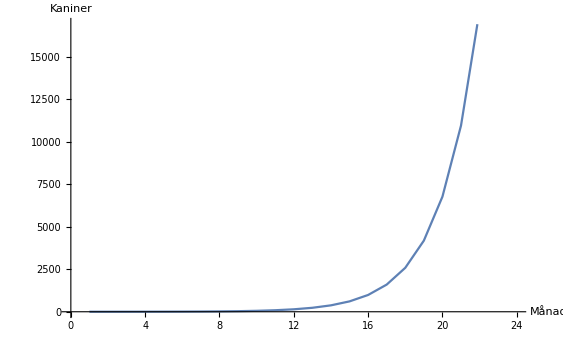

2.B) Undersök talföljden och diskutera tillväxtakten

Talföljden ökar exponentiellt under alla månader utom dom 2 första. Då desto fler par det finns just den månaden, desto större blir tillväxten av par för nästa månad o.s.v. Vi utgår ifrån att använda Fibonaccis talföljd där  summa är summan av de 2 föregående talen, vilket illusterar tillväxten väldigt bra i detta fall.

2.C) Vilka begränsningar har modellen?

Modellen tar inte upp att det kan finnas andra faktorer som påverkar en minskning i tillväxten, såsom brist på mat/näring när förökning sker så snabbt. Samt problemet med rovdjur och andra livshotande faktorer.

Modellen antar att alla nya par föds som  X,Y men det kan lika gärna vara så att dom nya paren är av samma kön såsom X,X och Y,Y.

Modellen antar också att kaniner lever och förökar sig förevigt.

2.D) Hur kan man förbättra modellen?

Modellen kan förbättras genom att ta i hänsyn till det vi nämnde i fråga C. Alltså att inkludera att utomstående faktorer kan påverka tillväxten, såsom rovdjur, väder, brist på mat osv. Samt att modellen just nu antar att det föds lika många honor som hanar. Dock så ska detta vara en förenklad modell av verkligheten och om man skulle ta med dessa fakoterer så skulle problemet bli betydligt mer komplext.

## Kod

2.A) Beräkna talföljden och rita en graf över den.

Vi använder fibonaccis talföljd som är inbyggd i wolfram för att se hur många kaninerna kommer vara efter 24 månader.

```mathematica
Kaniner= Fibonacci[24]
```

46368

Här räknas det ut hur förökningen kommer att se ut under de kommande 24 månaderna:

```mathematica
Table[Fibonacci[n], {n,24}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368}

Här är illustreras resultatet med en graf:

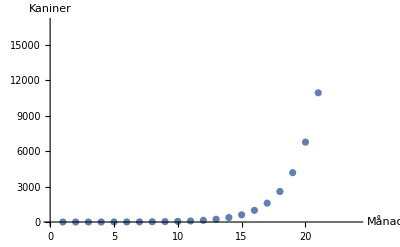

```mathematica
ListPlot[Table[Fibonacci[n], {n, 24}], AxesLabel-> {"Månad","Kaniner"}]
```

Då Listploten är begränsad till att bara illustrera månader så kan en Listlineplot vara mer relevant om man vill få en insyn på mindre intervall såsom till exempel dagar, veckor och så vidare.

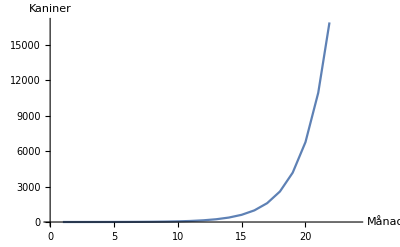

```mathematica
ListLinePlot[Table[Fibonacci[n], {n, 24}], AxesLabel-> {"Månad","Kaniner"}]
```

Referenser

## Referenser och Hjälpmedel

Datorövning 2 dokument

Datorövning 1 dokument

https://reference.wolfram.com/language/ref/Reduce.html

https://reference.wolfram.com/language/ref/Table.html

https://reference.wolfram.com/language/ref/ListPlot.html 

https://sv.wikipedia.org/wiki/Differensekvation 

https://reference.wolfram.com/language/ref/Fibonacci.html